# Aviation Formulae

## Preliminaries

## The Atmosphere

The atmosphere is a bipartite model, with one descriptor that applies from ground to the bottom of the stratosphere, and another descriptor that applies in the stratosphere.  This is beause the temperature changes below the stratosphere and is constant in the stratosphere.

### Below the stratosphere

The stratosphere begins at 11000 meters and goes up far beyond the maximum altitude of commercial aircraft.  11000 meters is 36089 feet.  To incorporate the altitude dependence of temperature and its influence on pressure and density, this factor of theta will need to be computed frequently.  It is definited for STP (Standard Temperature and Pressure) atmosphere as (first for feet and then for meters) as

```mathematica
thetafeet=(1-6.875 10^-6 h)
```

1-6.875×10^-6 h

```mathematica
thetameters=(1-2.255 10^-5 h)
```

1-0.00002255 h

We will need the air density as a function of altitude for almost all of our calculations.  At sea level and 15 degrees C, the density is 1.2922 kg/m^3.  There are correction factors for nonstandard sea level temperatures and lapse rates (rate of temp change with altitude), they will be ignored for now. Solving the ideal gas equilirium condition below 11 kilometers gives the air density ratio (the ratio of density at altitude to density at sea level) as

```mathematica
densitylowfeet[h_]:=(1-6.875 10^-6 h)^4.2541
```

```mathematica
densitylowmeters[h_]:=(1-2.255 10^-5 h)^4.2541
```

### In the stratosphere

In the stratosphere (above 11000 meters) the equation of state changes, and the density ratio is given by:

```mathematica
densitystratfeet[h_]:=0.2971 Exp[-(h-36089)/20806.7]
```

```mathematica
densitystratmeters[h_]:=0.2971 Exp[-(h-11000)/6341.9]
```

```mathematica
densitymeters[h_]:=If[h<11000, densitylowmeters[h],densitystratmeters[h]]
```

### A picture

```mathematica
loweraltitude=Plot[densitylowmeters, {h,0,11000},PlotRange->{{0,15000},{0,1}}];
upperaltitude=Plot[densitystratmeters, {h,11000,15000}];
```

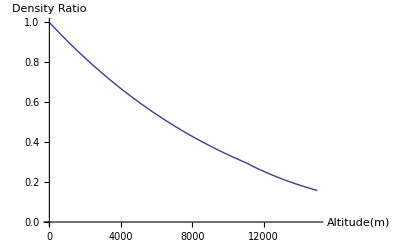

```mathematica
Plot[densitymeters[h], {h,0,15000},AxesLabel->{"Altitude(m)", "Density Ratio"},PlotRange->{{0,15000},{0,1}}]
```

## Aircraft Performance

## Lift and Drag

A set of numbers is required to quantify the aerodynamic performance of a given aircraft independent of its engine  parameters under several different operating regimes (climb, cruise, flaps at various extensions, dirty (gear down), clean, etc).  The simplest approximation to the Lift/Drag relationship is a quadratic equation.  In addition, we need the effective wing area to compute lift, the reference aircraft mass (to know how much lift we need to stay aloft), the speed of the aircraft (which affects aerodynamic forces), the density of the atmosphere (to compute magnitudes of lift and drag), the acceleration of the aircraft (banked or not), and the effect of departures from effective mass.

The lift is given by the fraction of the "flat plane" force required to balance the force of gravity on the aircraft where m is the mass of the aircraft in kg, h is altitude (meters), v is speed in meters/sec, s is wing area in meters^2, and ϕ is the bank angle. (banking reduces the effective lifting area, thereby increasing the amount of lift required per unit area).

```mathematica
cl[m_,v_,h_,ϕ_,s_]:=2 m 9.80665/(densitymeters[h] v^2 s Cos[ϕ])
```

Cos[ϕ] can be computed as a function of parametric representations of x and y velocities and accelerations inducing the banking after one calculates the parametric radius of curvature of the trajectory.  The turn radius R is given by:

rxy[vx_,vy_,ax_,ay_]:=(vx^2+vy^2)^(3/2)/(vx ay-vy ax)

```mathematica
rxy[vx,vy,ax,ay]
```

((vx^2+vy^2)^(3/2))/(ay vx-ax vy)

A sample of a radius at typical speeds and a very gentle acceleration yields a big radius:

```mathematica
rxy[240,0,0,1]
```

57600

A harder bank yields a smaller circle

```mathematica
rxy[240,0,0,10]
```

5760

The approximation to second order for the cosine of the arctan of v^2/gR (the bank angle) is:

```mathematica
cphi[vx_,vy_,ax_,ay_]:=Series[Cos[ArcTan[(vx^2+vy^2)/(9.80665 rxy[vx,vy,ax,ay])]], {x,0,2}]
```

```mathematica
cphi[vx,vy,ax,ay]
```

1/(√(1+(0.0103982 (ay vx-ax vy)^2)/(vx^2+vy^2)))

A sample of a slight bank:

```mathematica
cphi[240,0,0,1]
```

0.994841

Banking hard enough to produce a centripetal force equal to that of gravity should produce a 45 degree bank angle and therefore a cosine equal to 1/Sqrt[2]

```mathematica
cphi[240,0,0,9.8]
```

0.707347

Now the lift coefficient is fully parametrized

```mathematica
cl[m_,h_,s_,vx_,vy_,ax_,ay_]:=2 m 9.80665/(densitymeters[h] (vx^2+vy^2) s cphi[vx,vy,ax,ay])
```

```mathematica
cl[m,h,s,vx,vy,ax,ay]
```

(19.6133 m √(1+(0.0103982 (ay vx-ax vy)^2)/(vx^2+vy^2)))/(s (vx^2+vy^2) If[h<11000,densitylowmeters[h],densitystratmeters[h]])

But we need drag to know how much thrust (and therefore how much fuel we need to burn) is required.  The coefficients of drag and lift are related to lowest order by the "drag polar"

```mathematica
cd[cd0_,cd2_,m_,h_,vx_,vy_,ax_,ay_,s_]:=cd0+cd2 cl[m,h,s,vx,vy,ax,ay]^2
```

```mathematica
cd[cd0,cd2,m,h,vx,vy,ax,ay,s]
```

cd0+(384.682 cd2 m^2 (1+(0.0103982 (ay vx-ax vy)^2)/(vx^2+vy^2)))/(s^2 (vx^2+vy^2)^2 If[h<11000,densitylowmeters[h],densitystratmeters[h]]^2)

The drag is given by (in MKS units, where speed v is in m/sec, wing area s in meters^2, altitude h in meters)

```mathematica
drag[h_,s_, cd0_,cd2_,m_,vx_,vy_,ax_,ay_]:=1/2 densitymeters[h] (vx^2+vy^2) s cd[cd0,cd2,m,h,vx,vy,ax,ay,s]
```

```mathematica
drag[h,s,cd0,cd2,m,vx,vy,ax,ay]
```

1/2 s (vx^2+vy^2) (cd0+(384.682 cd2 m^2 (1+(0.0103982 (ay vx-ax vy)^2)/(vx^2+vy^2)))/(s^2 (vx^2+vy^2)^2 If[h<11000,densitylowmeters[h],densitystratmeters[h]]^2)) If[h<11000,densitylowmeters[h],densitystratmeters[h]]

```mathematica
drag[10000,  124.65, .0254, .0358,65300,240,0,0,0]
```

Power::infy: Infinite expression 1/0 encountered.

42874.9

## Thrust

The maximum climb thrust is a quadratic polynomial in altitude (h).  It is given in general form as:

```mathematica
maxclimbthrust[c1_,c2_,c3_,h_]:=c1-c1/c2 h+c1 c3 h^2
```

where thrust is in Newtons (N), altitude (h) in ft,  c1 is in Newtons, c1/c2 in Newton-ft, c1 c3 in Newton/ft^2.  For our B-737-800, c1 = 146590 N, c2 = 53872 ft, c3 = 0.30453 10^-9/ft^2.

```mathematica
maxclimbthrust[146590,53872,0.30453 10^(-10),h]
```

146590-(73295 h)/26936+4.46411×10^-6 h^2

A version of this where altitude is measured in meters is given by:

```mathematica
maxclimbthrustmetric[c1_,c2_,c3_,h_]:=c1-c1/c2 h 3.28084+c1 c3 h^2 10.7639
```

For the Boeing 737-800,

```mathematica
t737=maxclimbthrustmetric[146590,53872,0.30453 10^(-10),h]
```

146590-8.92743 h+0.0000480512 h^2

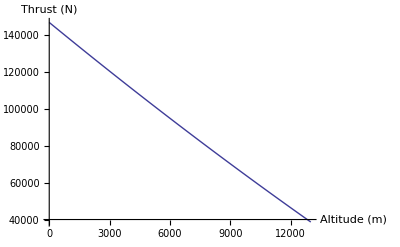

```mathematica
Plot[t737, {h, 0, 13000}, AxesLabel->{"Altitude (m)", "Thrust (N)"}]
```

Or, plotted as a fraction of maximum sea level thrust it becomes clear that there will be a maximum altitude beyond which there is insufficient thrust to overcome drag and continue climbing:

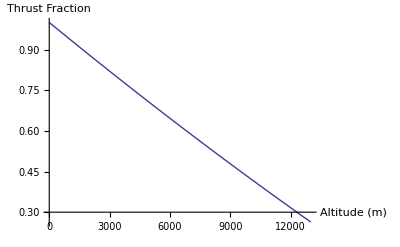

```mathematica
Plot[t737/146590., {h, 0, 13000},  AxesLabel->{"Altitude (m)", "Thrust Fraction"}]
```

## Constraints